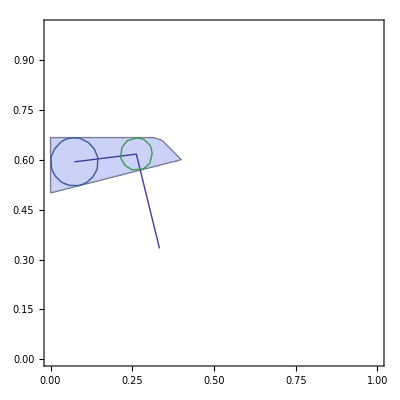

```mathematica
inp=Import["/Users/astyskin/Documents/workspace/decision/output.txt","Table"];
cons =TakeWhile[inp,#≠{-1}&];
points=Reverse[TakeWhile[Reverse[inp],#≠{-1}&]];
circle[a_,b_]:=Map[((a-#[[2]])^2+(b-#[[3]])^2==#[[1]]^2)&,points];

reg=RegionPlot[And@@Map[(#.{-1,a,b})>0&,cons],{a,0,1},{b,0,1}];
way=ListLinePlot[Map[Rest,points],PlotRange->{{0,1},{0,1}}];
cir=ContourPlot[Evaluate[circle[a,b]],{a,0,1},{b,0,1}];
Show[reg,way,cir]
```